```mathematica
f[x_]=(Cos[2 x +3]+1)^Log[3 x+7];a=-1;b=3;h=0.2;
```

```mathematica
(*Вычислим количество значений производной на отрезке[-1,3] с шагом h=0,2.*)
```

```mathematica
n=(b-a)/h;
```

```mathematica
(*Формула второго порядка точности:*)
pro1 [x_] = (f[x+h]-f[x-h])/(2h);
```

```mathematica
(*Составим таблицу:*)
Table[{a+h*i,pro1[a+h*i]},{i,0,n}]
```

{{-1.,-2.04443},{-0.8,-2.91551},{-0.6,-2.65183},{-0.4,-1.56685},{-0.2,-0.524553},{0.,-0.0652007},{0.2,0.0924852},{0.4,0.57492},{0.6,1.82225},{0.8,3.86538},{1.,6.0618},{1.2,7.12784},{1.4,5.79705},{1.6,1.86596},{1.8,-3.21056},{2.,-6.97808},{2.2,-7.6893},{2.4,-5.63972},{2.6,-2.76195},{2.8,-0.815753},{3.,-0.112093}}

```mathematica
(*б)
Нарисуем график производной,точки,которые мы высчитали с помощью функции D пакета Mathematica,точки,соответствующие приближенным значениям производной.
*)
dif[x_]=D[f[x],x];
```

```mathematica
graphic1 = Plot[dif[x],{x,a,b},PlotRange->{{-1,3}, {-100, 100}}];graphic2 = ListPlot[Table[{a+h*i,dif[a+h*i]},{i,0,n}], PlotStyle->Red];graphic3 = ListPlot[Table[{a+h*i,pro1[a+h*i]},{i,0,n}], PlotStyle->Green];
```

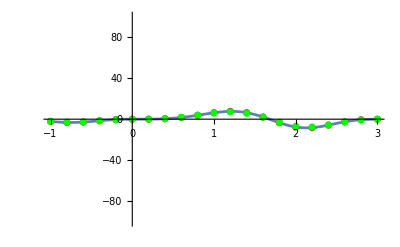

```mathematica
Show[graphic1, graphic2, graphic3]
```